# Verdampfungswäre

## 1. Bestimmung des Wasserwertes W vom Dewar - Gefäß

1. Auffüllen des Dewar-Gefäßes mit klaten Wasser T_k

2.  Nach ein paar Minuten wieder ausleeren

```mathematica
mBecher = 0.02(*kg*);
dmBecher=0.001(*kg*);
mGesamt =0.2(*kg*);
dmGesamt=0.002(*kg*);
mWasserWarm = mGesamt - mBecher;
dmWasserWarm = dmGesamt+dmBecher;
```

3.  Warmes Wasser 3 min messen (T/°C, t/s)

```mathematica
dataW = {{"t/s", 0, 30, 60, 90, 120, 150, 180, 230, 280}, {"T/°C", 6, 5.4, 5, 4, 5, 4.3, 3, 2, 3}}(*für Warmes Wasser*);
ddataW = {{0}, {0}}(*Fehler*);
```

4.Einschütten von warmen Wasser T_w, m_w

```mathematica
tm= 200
```

200

```mathematica
dataM = {{"t/s", 300, 330, 360, 390, 440, 490, 530, 620, 700}, {"T/°C", 2, 1.8, 1.7, 1.4, 1.2, 1, 1, 1, 1}}(*für Gemischtes Wasser*);
ddataW = {{0}, {0}}(*Fehler*);
```

5. Differenztemperatur zurückrechnen

```mathematica
Table[{dataW[[1,i]],dataW[[2,i]]},{i,2,Dimensions[dataW][[2]]}];
```

```mathematica
fitWdata=Table[{dataW[[1,i]],dataW[[2,i]]},{i,2,Dimensions[dataW][[2]]}];
fitW = LinearModelFit[fitWdata,x,x]
```

FittedModel[5.78756-0.0126211 x]

```mathematica
fitMdata=Table[{dataM[[1,i]],dataM[[2,i]]},{i,2,Dimensions[dataM][[2]]}];
fitM = LinearModelFit[fitMdata,x,x]
```

FittedModel[2.5189-0.00254088 x]

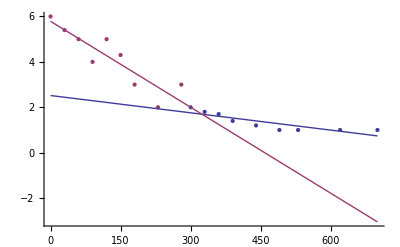

```mathematica
Show[ListPlot[{fitMdata,fitWdata}],Plot[{fitM[i],fitW[i]},{i,0,700}]]
```

```mathematica
Tm=fitM[tm]
dTm = 0;
Tw = fitW[tm]
dTw=0;
Tk=0.2;
dTk=1;
```

2.01072

3.26334

```mathematica
c0=1(*kcal*);
dc0=0;
```

```mathematica
GError[a_,b_,c_]:= (Total[Map[Abs,MapThread[D,{Table[a,{i,1,Length[b]}],b}]]*c]);
W[mw_,co_,Tw_,Tm_,Tk_,dmw_,dco_,dTm_,dTw_,dTk_]:=Module[{vmw,vco,vTm,vTw,vTk,vdmw,vdco,vdTm,vdTw,vdTk,f,fe},
f=(vmw vco (vTw-vTm))/(vTm-vTk);
fe=GError[f,{vmw,vco,vTm,vTw,vTk},{vdmw,vdco,vdTm,vdTw,vdTk}];
{f,fe}/.{vmw->mw,vco->co,vTm->Tm,vTw->Tw,vTk->Tk,vdmw->dmw,vdco->dco,vdTm->dTm,vdTw->dTw,vdTk->dTk}]
```

```mathematica
WW=W[mWasserWarm,c0,Tw,Tm,Tk,dmWasserWarm,dc0,dTm,dTw,dTk]
```

{0.12452,0.0708437}

## 2. Bestimmung der Verdampfungswärme von Wasser

Wiegen der leeren Thermosflasche

```mathematica
m0=0.5(*kg*)
dm0=0.1(*kg*)
```

0.5

0.1

Füllen mit klatem Wasser

```mathematica
mMitWasser=2.5(*kg*)
dmMitWasser = 0.3(*kg*)
m1 = mMitWasser -m0
dm1 = dm0 + dmMitWasser
```

2.5

0.3

2.

0.4

Wasserdampf einleiten bis ~50 °C, vorher schon T messen , Zwickelabgleich für T1 T2

```mathematica
T1 = 20(*°C*)
dT1 = 1
T2 = 50
dT2 = 1
```

20

1

30

1

Wiegen mit warmem Wasser

```mathematica
mMitWarmemWasser = 2.7
dmMitWarmemWasser = 0.3
m2 = mMitWarmemWasser - mMitWasser
dm2 = dmMitWarmemWasser - dmMitWasser
```

2.7

0.3

0.2

0.

```mathematica
r[vm1_,vco_,vW_,vT2_,vT1_,vm2_,vdm1_,vdco_,vdW_,vdT2_,vdT1_,vdm2_]:=Module[{f,fe,fr,m1,c0,W,T2,T1,m2,dm1,dc0,dW,dT2,dT1,dm2},
f=((m1 c0 + W)(T2-T1))/m2-(100-T2)c0;
fe=GError[f,{m1,c0,W,T2,T1,m2},{dm1,dc0,dW,dT2,dT1,dm2}];
fr = ((dm1 c0 +dW)/(c0 +W)+dT1/(T2-T1)+dT2/(T2-T1)+dm2/m2)(f+c0(100-T2))+c0 dT2;
{f,fe,fr}/.{m1->vm1,c0->vco,W->vW,T2->vT2,T1->vT1,m2->vm2,dm1->vdm1,dc0->vdco,dW->vdW,dT2->vdT2,dT1->vdT1,dm2->vdm2}]
```

```mathematica
r[m1,c0,WW[[1]],T2,T1,m2,dm1,dc0,WW[[2]],dT2,dT1,dm2]
```

{36.226,45.7874,66.7227}